## Data Input & Adjacency Matrix Creation

```mathematica
data=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21\\UMaine\\F21UMaineNetworkReady.xlsx"][[1]];  (* importing NetworkReady data *)
SetDirectory[NotebookDirectory[]];  (* makes it so any files exported wil be saved in the same folder that this file is located in *)

data//MatrixForm;

(* defines the number of concepts & expressions on the survey, as well as the number of students that we are looking at *)
nConc=Dimensions[data][[2]]; 
nExp=20;
nStu=Dimensions[data][[1]]-1;

(* makes a list of nExp x nExp matrices, one per student, where we will collect all of the pairs of expressions that each individual student used together *)
stuList=Table[0,{i,1,nStu},{j,1,nExp},{k,1,nExp}];

(* These nested for loops will count each pair of expressions used only once per student. I.e., if one student used the same pair of expressions for multiple concepts, it will only count as one use of the pair in the final data *)
For[i=1,i≤nStu,i++,
For[j=1,j≤nConc,j++,
For[k=1,k≤nExp,k++,
For[l=1,l≤nExp,l++,
(* changes all single-letter entries into single-entry lists.  This is done because ContainsAny[] requires a list as input *)
If[Length[LetterNumber[StringDelete[data[[i+1,j]],","]]]==0,data[[i+1,j]]={data[[i+1,j]]}];

(* goes through each combination of letters and compares; updates table4 entries with the number of times the pairs appear together in the data *)
If[ContainsAny[LetterNumber[StringDelete[data[[i+1,j]],","]],{k}]&&ContainsAny[LetterNumber[StringDelete[data[[i+1,j]],","]],{l}]&&stuList[[i,k,l]]==0,stuList[[i,k,l]]++(*;pairs[[i,k,l]]++*)]   
]
]
]
]

(* remove the 1s on the diagonal *)
For[k=1,k≤nStu,k++,
For[i=1,i≤nExp,i++,
For[j=1,j≤nExp,j++,
If[i==j && stuList[[k,i,j]]==1,
stuList[[k,i,j]]--
]
]
]
]
```

## Making Graphs

```mathematica
vertices={Property["a",VertexLabels->OverVector["v"]],Property["b",VertexLabels->OverHat["j"]],Property["c",VertexLabels->OverHat["S_z"]],Property["d",VertexLabels->"f(x)"],Property["e",VertexLabels->"|ψ⟩"],Property["f",VertexLabels->"|E_2⟩"],Property["g",VertexLabels->"⟨E_1|"],Property["h",VertexLabels->"ψ(x)"],Property["i",VertexLabels->"ψ^*(x)"],Property["j",VertexLabels->"φ_3(x)"],Property["k",VertexLabels->"φ_4^*(x)"],Property["l",VertexLabels->OverVector["u"]·OverVector["v"]],Property["m",VertexLabels->"⟨ψ|ψ⟩"],Property["n",VertexLabels->"⟨E_3|ψ⟩"],Property["o",VertexLabels->"∫ψ^*ψdx"],Property["p",VertexLabels->"∫φ_1^*ψdx"],Property["q",VertexLabels->"|⟨E_4|ψ⟩|^2"],Property["r",VertexLabels->"|∫ψ^*ψdx|^2"],Property["s",VertexLabels->"|∫φ_2^*ψdx|^2"],Property["t",VertexLabels->"⟨ψ|"]};
vertexLabels={OverVector["v"],OverHat["j"],OverHat["S_z"],"f(x)","|ψ⟩","|E_2⟩","⟨E_1|","ψ(x)","ψ^*(x)","φ_3(x)","φ_4^*(x)",OverVector["u"]·OverVector["v"],"⟨ψ|ψ⟩","⟨E_3|ψ⟩","∫ψ^*ψdx","∫φ_1^*ψdx","|⟨E_4|ψ⟩|^2","|∫ψ^*ψdx|^2","|∫φ_2^*ψdx|^2","⟨ψ|"};

g=AdjacencyGraph[vertexLabels,stuList[[1]],VertexLabels->Automatic];
circle[n_]:=Table[{Cos[2*Pi/n*u],Sin[2*Pi/n*u]},{u,1,n}]

stuGraphs=Table[0,{i,1,nStu}];
stuGraphsBig=Table[0,{i,1,nStu}];
stuGraphsBigC=Table[0,{i,1,nStu}];
stuGraphsBigCNum=Table[0,{i,1,nStu}];

For[i=1,i≤nStu,i++,
(* creates the basic networks *)
stuGraphs[[i]]=AdjacencyGraph[vertexLabels,stuList[[i]],VertexLabels->Automatic];
(* creates the basic networks with larger vertices and frames *)
stuGraphsBig[[i]]=AdjacencyGraph[vertexLabels,stuList[[i]],VertexLabels->Automatic,VertexSize->Large,ImageSize->Large,VertexLabelStyle->20,Frame->{{True,False},{True,False}},FrameStyle->LightGray];
(* creates the individual networks, but arrayed in a circle for ease of comparison *)
stuGraphsBigC[[i]]=AdjacencyGraph[vertexLabels,stuList[[i]],VertexLabels->Automatic,VertexSize->Large,ImageSize->Large,VertexLabelStyle->15,VertexCoordinates->circle[nExp]];
(* creates the circular networks, but now with numerical labels for each in the middle of each circle *)
stuGraphsBigCNum[[i]]=Show[
AdjacencyGraph[vertexLabels,stuList[[i]],VertexLabels->Automatic,VertexSize->Large,ImageSize->Large,VertexLabelStyle->15,VertexCoordinates->circle[nExp]],
Graphics[Text[Style["B"<>ToString[i],FontSize->50,Bold]]]
]
]

(* creates a list of the filenames for each exported network PNG file *)
graphFilenames=Table["UMainestB"<>ToString[i++]<>".png",{i,1,nStu}];

(*
(* exports the circular, numbered networks *)
For[i=1,i≤nStu,i++,
Export[graphFilenames[[i]],stuGraphsBigCNum[[i]]]
]
```

```mathematica
(* animation that cycles through all of the circular, numbered networks *)
ListAnimate[stuGraphsBigCNum,1]
```

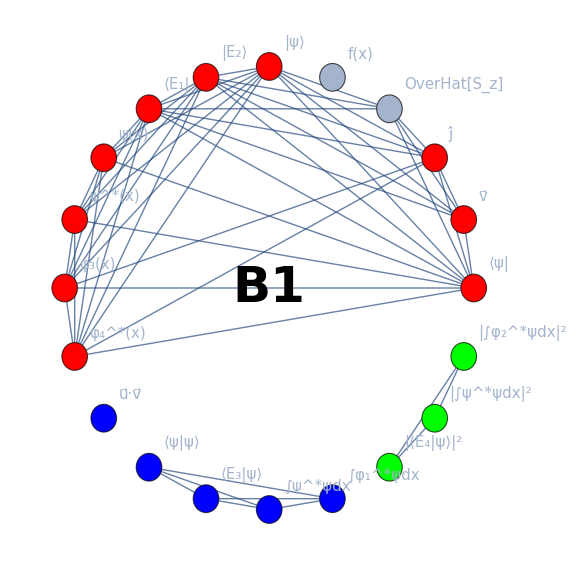

```mathematica
graphsPCA=Table[0,nStu];

edgeTab=Table[0,nExp,nExp];

edgeLists=Table[0,nStu];

For[i=1,i<=nStu,i++,
edgeLists[[i]]=EdgeList[stuGraphs[[i]]]
]

For[i=1,i<=nExp,i++,
For[j=1,j<=nExp,j++,
edgeTab[[i,j]]=vertexLabels[[i]]<->vertexLabels[[j]]
]
]

For[i=1,i<=nStu,i++,
graphsPCA[[i]]=Show[
AdjacencyGraph[vertexLabels,stuList[[i]],
VertexLabels->Automatic,
VertexSize->Large,
ImageSize->Large,
VertexLabelStyle->15,
VertexCoordinates->circle[nExp],
VertexStyle->{"|ψ⟩"->Red,OverVector["v"]->Red,OverHat["j"]->Red,"|E_2⟩"->Red,"⟨E_1|"->Red,"ψ(x)"->Red,"ψ^*(x)"->Red,"φ_3(x)"->Red,"φ_4^*(x)"->Red,"⟨ψ|"->Red,OverVector["u"]·OverVector["v"]->Blue,"⟨ψ|ψ⟩"->Blue,"⟨E_3|ψ⟩"->Blue,"∫ψ^*ψdx"->Blue,"∫φ_1^*ψdx"->Blue,"|⟨E_4|ψ⟩|^2"->Green,"|∫ψ^*ψdx|^2"->Green,"|∫φ_2^*ψdx|^2"->Green},
EdgeStyle->Automatic
],
Graphics[Text[Style["B"<>ToString[i],FontSize->50,Bold]]]
]
]

singVertCol={"|ψ⟩"->Red,OverVector["v"]->Red,OverHat["j"]->Red,"|E_2⟩"->Red,"⟨E_1|"->Red,"ψ(x)"->Red,"ψ^*(x)"->Red,"φ_3(x)"->Red,"φ_4^*(x)"->Red,"⟨ψ|"->Red};
doubVertCol={OverVector["u"]·OverVector["v"]->Blue,"⟨ψ|ψ⟩"->Blue,"⟨E_3|ψ⟩"->Blue,"∫ψ^*ψdx"->Blue,"∫φ_1^*ψdx"->Blue};
squVertCol={"|⟨E_4|ψ⟩|^2"->Green,"|∫ψ^*ψdx|^2"->Green,"|∫φ_2^*ψdx|^2"->Green};



edgeLists//MatrixForm;

edgeTab//MatrixForm;
graphsPCA[[1]]
```

```mathematica
For[i=1,i<=nStu,i++,
graphsPCA[[i]]=Show[
AdjacencyGraph[vertexLabels,stuList[[i]],
VertexLabels->Automatic,
VertexSize->Large,
ImageSize->Large,
VertexLabelStyle->15,
VertexCoordinates->circle[nExp],
VertexStyle->Join[singVertCol,doubVertCol,squVertCol],
EdgeStyle->Automatic
],
Graphics[Text[Style["B"<>ToString[i],FontSize->50,Bold]]]
]
]
```

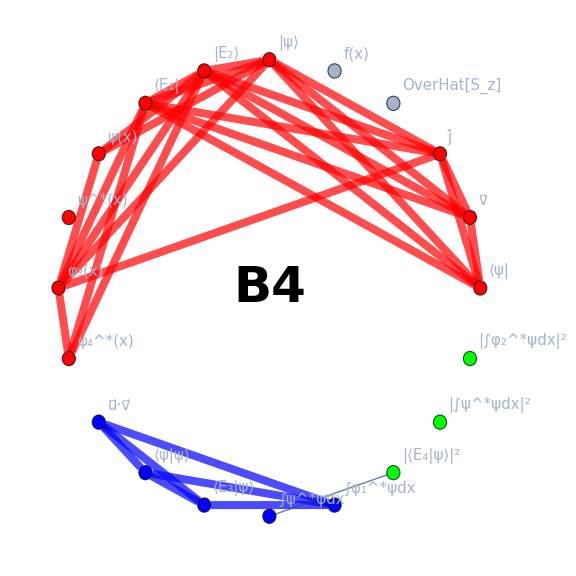

```mathematica
(* This code down here creates graphs with the edges also color-coded to the group of expressions they belong in *)

(* start by creating matrices with every edge that exists within the predefined communities *)
singEdges=Delete[Transpose[Delete[edgeTab,{{3},{4},{12},{13},{14},{15},{16},{17},{18},{19}}]],{{3},{4},{12},{13},{14},{15},{16},{17},{18},{19}}];

doubEdges=Delete[Transpose[Delete[edgeTab,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{17},{18},{19},{20}}]],{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{17},{18},{19},{20}}];

squEdges=Delete[Transpose[Delete[edgeTab,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{20}}]],{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{20}}];


(* here we create a list that contains every other edge that could exist within the networks, meaning those between or entirely outside of the predefined communities *)
nonCommEdges=Complement[Catenate[edgeTab],Catenate[singEdges],Catenate[doubEdges],Catenate[squEdges]];


edgeStyles=Table[{},nStu];

For[i=1,i<=nStu,i++,
For[j=1,j<=Length@edgeLists[[i]],j++,
For[k=1,k<=Length@singEdges,k++,
(* these go through and fill in the "edgeStyles" lists with the edges and their associated colors *)
If[ContainsAny[{edgeLists[[i,j]]},singEdges[[All,k]]]||ContainsAny[{edgeLists[[i,j]]},singEdges[[k,All]]],
edgeStyles[[i]]=Append[edgeStyles[[i]],edgeLists[[i,j]]->{Red,Thickness[0.01]}]
]
];
For[k=1,k<=Length@doubEdges,k++,
If[ContainsAny[{edgeLists[[i,j]]},doubEdges[[All,k]]]||ContainsAny[{edgeLists[[i,j]]},doubEdges[[k,All]]],
edgeStyles[[i]]=Append[edgeStyles[[i]],edgeLists[[i,j]]->{Blue,Thickness[0.01]}]
]
];
For[k=1,k<=Length@squEdges,k++,
If[ContainsAny[{edgeLists[[i,j]]},squEdges[[All,k]]]||ContainsAny[{edgeLists[[i,j]]},squEdges[[k,All]]],
edgeStyles[[i]]=Append[edgeStyles[[i]],edgeLists[[i,j]]->{Green,Thickness[0.01]}]
]
];

If[ContainsAny[{edgeLists[[i,j]]},nonCommEdges],
edgeStyles[[i]]=Append[edgeStyles[[i]],edgeLists[[i,j]]->{Black,Thickness[0.01]}]
]

];
(* without this little addition, it creates duplicates of each edge style, so this removes every other element of the lists *)
edgeStyles[[i]]=Drop[edgeStyles[[i]],{1,Length@edgeStyles[[i]],2}]
]

edgeStyles[[1]]//MatrixForm;

For[i=1,i<=nStu,i++,
graphsPCA[[i]]=Show[
AdjacencyGraph[vertexLabels,stuList[[i]],
VertexLabels->Automatic,
VertexSize->Medium,
ImageSize->Large,
VertexLabelStyle->15,
VertexCoordinates->circle[nExp],
VertexStyle->Join[singVertCol,doubVertCol,squVertCol],
EdgeStyle->edgeStyles[[i]]
],
Graphics[Text[Style["B"<>ToString[i],FontSize->50,Bold]]]
]
]

graphsPCA[[4]]
```

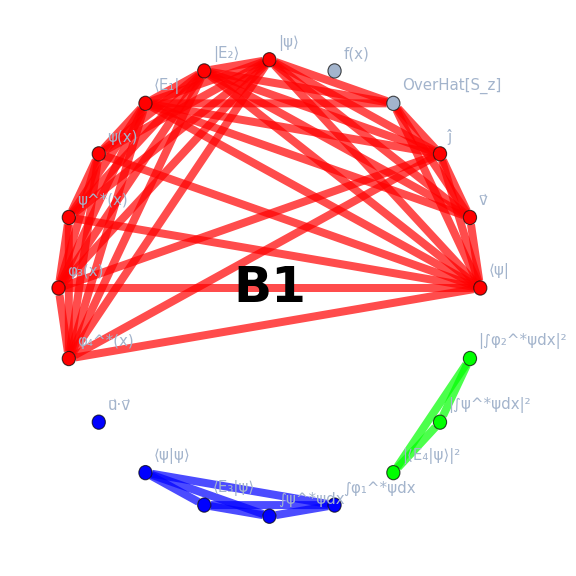
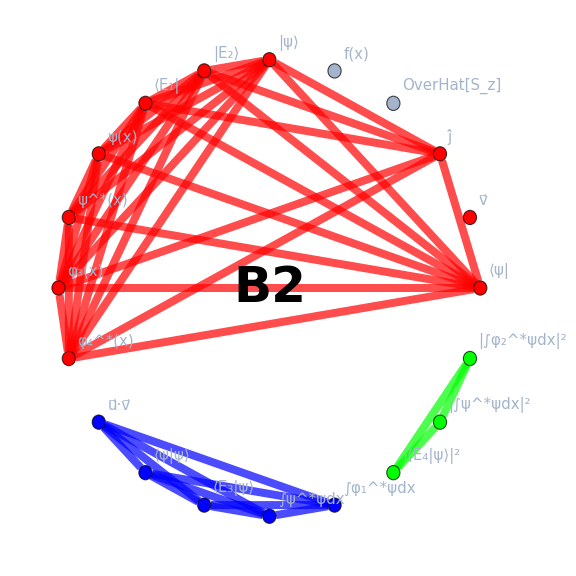
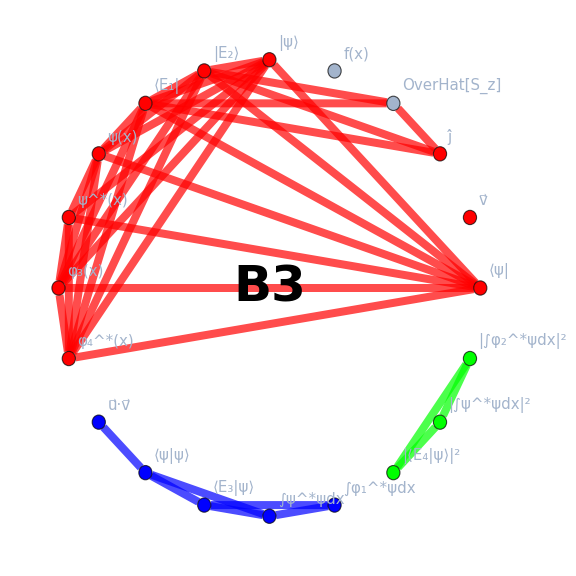
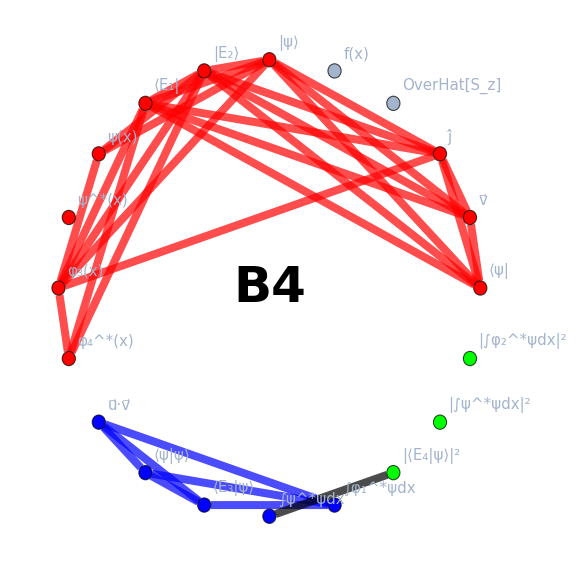
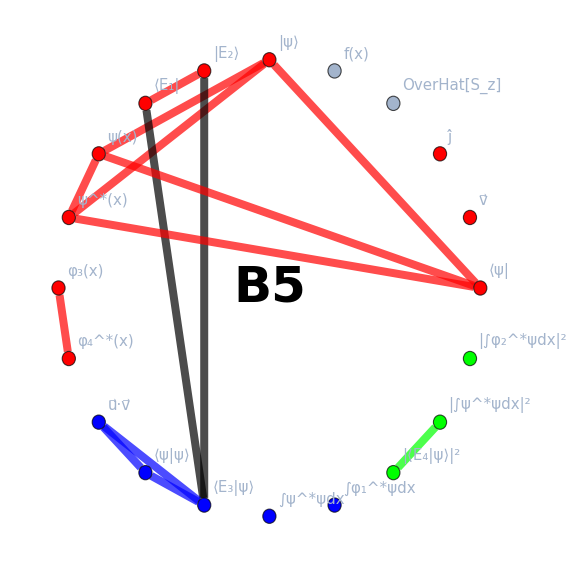
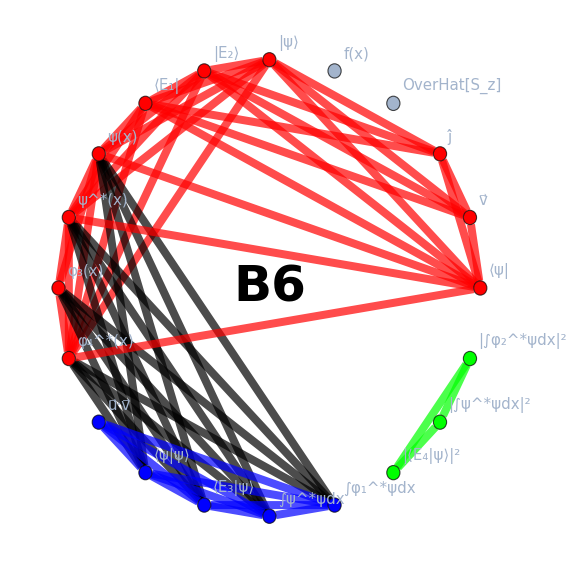
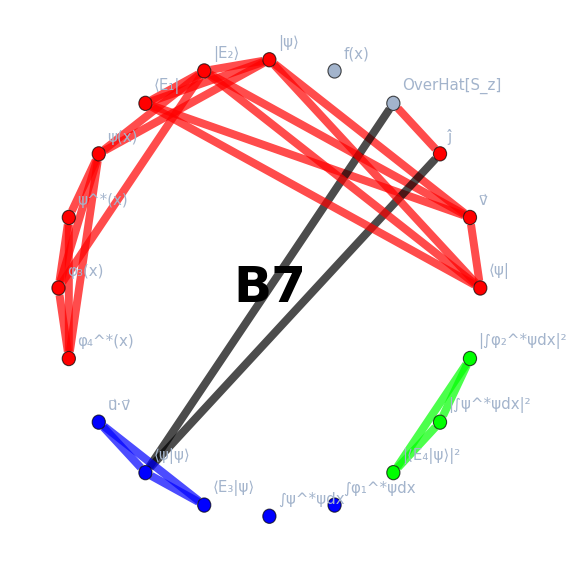
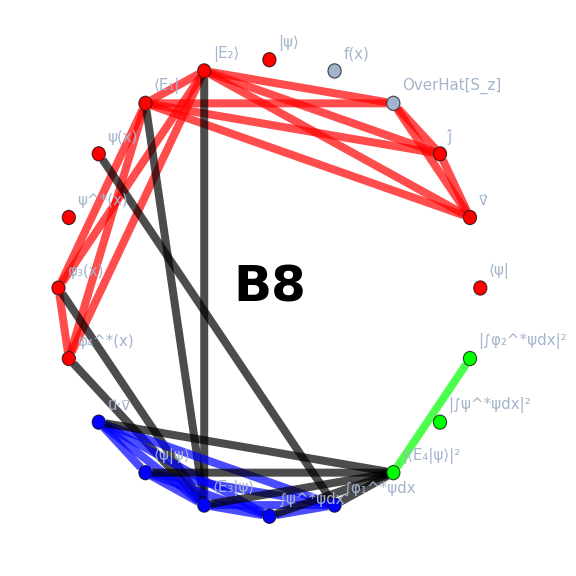

```mathematica
(* THIS CREATES GRAPHS WITH BLACK EDGES BETWEEN OR OUTSIDE OF COMMUNITIES *)




(* start by creating lists with every edge that exists within the predefined communities *)

singEdges=Catenate[Delete[Transpose[Delete[edgeTab,{{4},{12},{13},{14},{15},{16},{17},{18},{19}}]],{{4},{12},{13},{14},{15},{16},{17},{18},{19}}]];

doubEdges=Catenate[Delete[Transpose[Delete[edgeTab,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{17},{18},{19},{20}}]],{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{17},{18},{19},{20}}]];

squEdges=Catenate[Delete[Transpose[Delete[edgeTab,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{20}}]],{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{20}}]];


(* here we create a list that contains every other edge that could exist within the networks, meaning those between or entirely outside of the predefined communities *)
nonCommEdges=Complement[Catenate[edgeTab],singEdges,doubEdges,squEdges];

edgeStyles=Table[{},nStu];



For[i=1,i<=nStu,i++,
For[j=1,j<=Length@edgeLists[[i]],j++,
(* these go through and fill in the "edgeStyles" lists with the edges and their associated colors *)
If[ContainsAny[{edgeLists[[i,j]]},singEdges],
edgeStyles[[i]]=Append[edgeStyles[[i]],edgeLists[[i,j]]->{Red,Thickness[0.01]}]
];
If[ContainsAny[{edgeLists[[i,j]]},doubEdges],
edgeStyles[[i]]=Append[edgeStyles[[i]],edgeLists[[i,j]]->{Blue,Thickness[0.01]}]
];
If[ContainsAny[{edgeLists[[i,j]]},squEdges],
edgeStyles[[i]]=Append[edgeStyles[[i]],edgeLists[[i,j]]->{Green,Thickness[0.01]}]
];
If[ContainsAny[{edgeLists[[i,j]]},nonCommEdges],
edgeStyles[[i]]=Append[edgeStyles[[i]],edgeLists[[i,j]]->{Black,Thickness[0.01]}]
]
];
]

edgeStyles//MatrixForm;

For[i=1,i<=nStu,i++,
graphsPCA[[i]]=Show[
AdjacencyGraph[vertexLabels,stuList[[i]],
VertexLabels->Automatic,
VertexSize->Medium,
ImageSize->Large,
VertexLabelStyle->15,
VertexCoordinates->circle[nExp],
VertexStyle->Join[singVertCol,doubVertCol,squVertCol],
EdgeStyle->edgeStyles[[i]]
],
Graphics[Text[Style["B"<>ToString[i],FontSize->50,Bold]]]
]
]

graphsPCA

(* creates a list of the filenames for each exported network PNG file *)
colorGraphFilenames=Table["colorUMainestB"<>ToString[i++]<>".png",{i,1,nStu}];

(*
For[i=1,i≤nStu,i++,
Export[colorGraphFilenames[[i]],graphsPCA[[i]]]
]
```